```mathematica
conRodLength=3*crankshaftRadius (** [m] **)
crankshaftRadius= stroke/2. (** [m] **)
pistonHeight = 0.02 (** m **)
cylinderBore=0.0995
stroke= 0.079
compressionRatio = 10
bottomOfCylinderHead = (pistonPinPosition[0]-pistonPinPosition[Pi])+pistonHeight/2
compressionVolume=displacementVolume/(compressionRatio-1)
displacementVolume=Pi*((cylinderBore/2)^2)*(pistonPinPosition[0]-pistonPinPosition[Pi])
distancefromTDCpistonToCylinderHead=compressionVolume/(Pi*((cylinderBore/2)^2))

compressionRatio*compressionVolume;
compressionVolume+displacementVolume;
ratioCylBoreStroke=cylinderBore/stroke




pistonPinPosition[crankAngle_] := Module[{theta=crankAngle,position},
position=Sqrt[conRodLength^2-(crankshaftRadius^2)Sin[theta]^2]+crankshaftRadius*Cos[theta];
Return[position]
]

pistonPinVelocity[crankAngle_] := Module[{theta=crankAngle,velocity},
velocity=-crankshaftRadius*Sin[theta]-((crankshaftRadius^2*Cos[theta] Sin[theta])/Sqrt[(conRodLength^2-(crankshaftRadius*Sin[theta])^2)]);
Return[velocity]
]

pistonPinAcceleration[crankAngle_] := Module[{theta=crankAngle,acceleration},
acceleration=(-crankshaftRadius)*Cos[theta] - (crankshaftRadius^4*Cos[theta]^2*Sin[theta]^2)/(conRodLength^2 - crankshaftRadius^2*Sin[theta]^2)^(3/2) -(crankshaftRadius^2*Cos[theta]^2)/Sqrt[conRodLength^2 - crankshaftRadius^2*Sin[theta]^2] + (crankshaftRadius^2*Sin[theta]^2)/Sqrt[conRodLength^2 - crankshaftRadius^2*Sin[theta]^2];
Return[acceleration]
]

conRodPistonAngle[crankAngle_]:=Module[{gamma},
gamma=(crankshaftRadius/conRodLength)*Sin[crankAngle];

Return[gamma]
]

pistonClearanceHeight[crankAngle_,strk_,cRLength_,crnkRad_]:=Module[{height},
height=(strk/2)*((cRLength/crnkRad)+1-Cos[crankAngle]-Sqrt[(cRLength/crnkRad)^2-(Sin[crankAngle]^2)]);

Return[height]
]


pistonShape[bore_,height_]:=Module[{shape},
shape=Rectangle[Evaluate[{-bore/2.,-height/2.},{bore/2.,height/2.}]];

Return[shape]
]

conRodShape[width_]:=Module[{shape},
shape=Rectangle[Evaluate[{-width/2.,crankshaftRadius},{width/2.,conRodLength+crankshaftRadius}]];

Return[shape]
]

crankArmShape[width_]:=Module[{shape},
shape=Rectangle[Evaluate[{-width/2.,0},{width/2.,crankshaftRadius}]];

Return[shape]
]

shapeTranslation[shape_,translationVector_]:=Module[{translatedShape},
translatedShape=Translate[shape,translationVector];

Return[translatedShape]
]

shapeRotation[shape_,rotationVector_,point_]:=Module[{rotatedShape},
rotatedShape=Rotate[shape,rotationVector,point];

Return[rotatedShape]
]

Graphics[GeometricTransformation[pistonShape[2,0.5],{0,0}]];

Graphics[shapeTranslation[pistonShape[2,0.5],{0,0}]];
Graphics[conRodShape[0.1,conRodLength]];
Graphics[crankArmShape[0.1,crankshaftRadius]];





Animate[Show[{Graphics[shapeTranslation[shapeRotation[conRodShape[0.01],(crankshaftRadius/conRodLength)* Sin[theta],{0,conRodLength+crankshaftRadius}],{0,Sqrt[conRodLength^2-(crankshaftRadius^2)*Sin[theta]^2]+crankshaftRadius*Cos[theta]-conRodLength-crankshaftRadius}]](** Con rod **),Graphics[shapeTranslation[pistonShape[cylinderBore,pistonHeight],{0,Sqrt[conRodLength^2-(crankshaftRadius^2)*Sin[theta]^2]+crankshaftRadius*Cos[theta]}]](** Piston **),Graphics[{Circle[{0,0},crankshaftRadius],Point[{crankshaftRadius*Cos[theta-Pi/2],crankshaftRadius*Sin[theta+Pi/2]}]}] (** Crankshaft **),
Graphics[shapeRotation[crankArmShape[0.008],-theta,{0,0}]](** Crank arm **),
Graphics[Text["TDC",{0,1.1*crankshaftRadius}]],Graphics[Text["BDC",{0,-1.1*crankshaftRadius}]](** Text **),
Graphics[Rectangle[{-cylinderBore/1.5,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2},{cylinderBore/1.5,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2+(0.25*stroke)}]](** Top of Cylinder **),
Graphics[Rectangle[{-cylinderBore/1.5,crankshaftRadius},{-cylinderBore/1.98,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2}]],Graphics[Rectangle[{cylinderBore/1.5,crankshaftRadius},{cylinderBore/1.98,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2}]](** Walls **)},
ImageSize->500,Axes->True,GridLines->Automatic,PlotRange->{{-2.2*crankshaftRadius,2.2*crankshaftRadius},{-crankshaftRadius*1.8,1.1*(crankshaftRadius+conRodLength+pistonHeight)}}],{theta,0,4Pi,Pi/256},AnimationRunning->False,DefaultDuration->3.5]

pistonClearanceHeight[Pi,stroke,conRodLength,crankshaftRadius]
```

0.1185

0.0395

0.02

0.0995

0.079

10

0.089

0.0000682528

0.000614275

0.00877778

1.25949

0.079

```mathematica
pistonPinPosition[Pi]
```

1.75

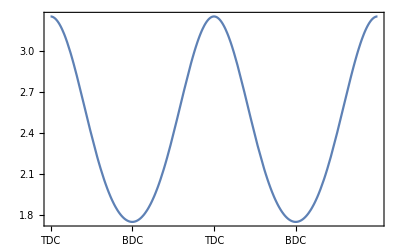
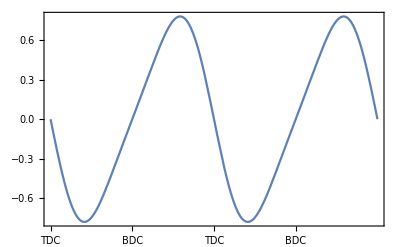
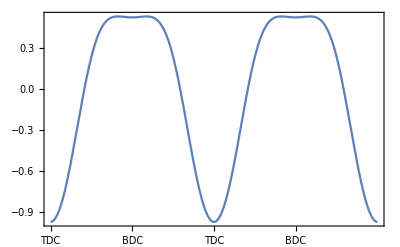

```mathematica
{Plot[pistonPinPosition[angle],{angle,0,4Pi},FrameTicks->{Automatic,{{{0,"TDC"},{Pi,"BDC"},{2Pi,"TDC"},{3Pi,"BDC"}},None}},Frame->True],Plot[pistonPinVelocity[angle],{angle,0,4Pi},FrameTicks->{Automatic,{{{0,"TDC"},{Pi,"BDC"},{2Pi,"TDC"},{3Pi,"BDC"}},None}},Frame->True],Plot[pistonPinAcceleration[angle],{angle,0,4Pi},FrameTicks->{Automatic,{{{0,"TDC"},{Pi,"BDC"},{2Pi,"TDC"},{3Pi,"BDC"}},None}},Frame->True]}
```

```mathematica
gif=Table[Show[{Graphics[shapeTranslation[shapeRotation[conRodShape[0.01],(crankshaftRadius/conRodLength)* Sin[theta],{0,conRodLength+crankshaftRadius}],{0,Sqrt[conRodLength^2-(crankshaftRadius^2)*Sin[theta]^2]+crankshaftRadius*Cos[theta]-conRodLength-crankshaftRadius}]](** Con rod **),Graphics[shapeTranslation[pistonShape[cylinderBore,pistonHeight],{0,Sqrt[conRodLength^2-(crankshaftRadius^2)*Sin[theta]^2]+crankshaftRadius*Cos[theta]}]](** Piston **),Graphics[{Circle[{0,0},crankshaftRadius],Point[{crankshaftRadius*Cos[theta-Pi/2],crankshaftRadius*Sin[theta+Pi/2]}]}] (** Crankshaft **),
Graphics[shapeRotation[crankArmShape[0.008],-theta,{0,0}]](** Crank arm **),
Graphics[Text["TDC",{0,1.1*crankshaftRadius}]],Graphics[Text["BDC",{0,-1.1*crankshaftRadius}]](** Text **),
Graphics[Rectangle[{-cylinderBore/1.5,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2},{cylinderBore/1.5,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2+(0.25*stroke)}]](** Top of Cylinder **),
Graphics[Rectangle[{-cylinderBore/1.5,crankshaftRadius},{-cylinderBore/1.98,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2}]],Graphics[Rectangle[{cylinderBore/1.5,crankshaftRadius},{cylinderBore/1.98,pistonPinPosition[0]+distancefromTDCpistonToCylinderHead+pistonHeight/2}]](** Walls **)},
ImageSize->500,Axes->True,GridLines->Automatic,PlotRange->{{-2.2*crankshaftRadius,2.2*crankshaftRadius},{-crankshaftRadius*1.8,1.1*(crankshaftRadius+conRodLength+pistonHeight)}}],{theta,0,4Pi,Pi/16}];
```

```mathematica
Export["C:\\Users\\wvboy\\Desktop\\pistongif.gif",gif,"GIF"]
```

C:\Users\wvboy\Desktop\pistongif.gif